```mathematica
ClearAll["Global`*"];
```

### Wprowadzenie wartości dla długości początkowej drutu ( "l_o" ).

```mathematica
lo=0.5; (*m*)
```

### Wykorzystanie prawa Hooka do obliczenia ciężaru zawieszonego na drucie ( "Q" ). “Δl” - przyrost długości drutu,“S” - pole przekroju poprzecznego drutu, “Ey” - modul Younga metalu, z którego zrobiony jest drut.

```mathematica
r1=Solve[Δl/lo==Q/S×1/Ey,Q];
```

### Obliczenie siły naciągu ( "F_n" ) działającej na drut. “α” - kąt jaki tworzy drut z kierunkiem pionu.

```mathematica
Fn =Sqrt[Q^2+ (Tan[α °]×Q)^2]/.r1[[1,1]];
```

### Obliczenie wydłużenia względnego ( "ϵ" ) wywołanego przez siłę naciągu.

```mathematica
ϵ=Fn/S×1/Ey//Simplify//PowerExpand;
```

### Sporządzenie wykresu obrazującego zależność wydłużenia względnego od kąta “α” dla Δl = .5 cm.

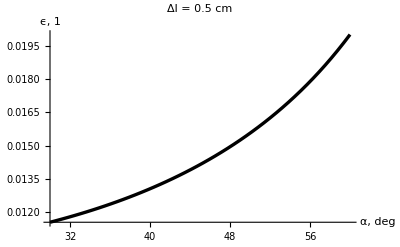

```mathematica
rys1=Plot[ϵ/.Δl->0.005,{α,30,60},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
PlotLabel->StyleForm[" Δl = 0.5 cm",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"α, deg","ϵ, 1"},
PlotStyle->{Black,Thickness[0.006]}]
```

### Sporządzenie wykresu obrazującego zależność wydłużenia względnego od kąta “α” dla Δl = 1 cm.

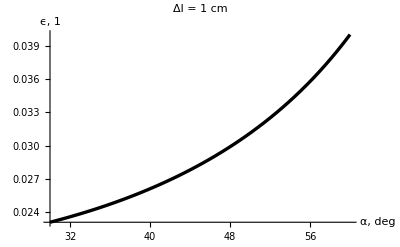

```mathematica
rys2=Plot[ϵ/.Δl->0.01,{α,30,60},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
PlotLabel->StyleForm[" Δl = 1 cm",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
AxesLabel->{"α, deg","ϵ, 1"},
PlotStyle->{Black,Thickness[0.006]}]
```